## Lecture 6: Data Collection, pre-processing (querying, cleaning, reduction, integrating) and storing

## Murilo da Silva Baptista murilo.baptista@abdn.ac.uk

## Overview

This lecture covers data collection, importing, manipulating, querying, and exporting.

Special attention to:

Collecting data in different formats (Excel, Tab, TXT, CSV and by API) and preprocessing it.

Useful upgrading (from lists to Datasets) and downgrading data structure transformations (Dataset to Associations, and Associations to Lists) with further preprocessing.

Pre-processing datasets (e.g. replacing and integrating) using Dataset formalism

Wolfram built-in Entities, Datasets and Examples Data.

Appendix : Integrating and Importing using API

# Importing data with Wolfram

format : e.g. AVI, BSON, CSV, GIF, HTML, JPEG, JSON, LATEX, Table, TAR, ZIP, etc

To see Elements, see documentation

## "Data" is the default element

Web Scraping of Free Data : You Tube video Wolfram Channel, by Andreas Lauschke

Patterns are very important formats in Mathematica, take a look at Link or check for material for Patterns placed in Myaberdeen.

# Specifying structure of the data to be imported

```mathematica
[see Documentation]
```

You can specify elements for the structure/type of data you want to Import or Export.

```mathematica
-Graphics-              -Graphics-
```

```mathematica
aa={1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
SetDirectory["/Users/murilo/Desktop"]
```

/Users/murilo/Desktop

```mathematica
Export["/Users/murilo/Desktop/a1data.csv",aa,"Data"]
```

/Users/murilo/Desktop/a1data.csv

```mathematica
Export["/Users/murilo/Desktop/a2data.csv",aa]
```

/Users/murilo/Desktop/a2data.csv

```mathematica
Import["/Users/murilo/Desktop/a2data.csv"]
```

{{1},{2},{3},{4},{5}}

```mathematica
aaa=RandomReal[{-1,1},{3,3}]
```

{{0.315636,0.523186,0.31277},{0.869152,0.0564501,0.303796},{-0.357825,0.167285,-0.880009}}

```mathematica
Export["/Users/murilo/Desktop/a1data.xlsx",aaa,"Data"]
```

/Users/murilo/Desktop/a1data.xlsx

"WL"—Wolfram Language source file (. wl, . m)

```mathematica
Export["/Users/murilo/Desktop/a1data.wl",rawDataset,"WL"]
```

/Users/murilo/Desktop/a1data.wl

```mathematica
rawDatasetImport=Import["/Users/murilo/Desktop/a1data.wl","WL"]
```

## Importing data as a Dataset with Keys

Description of Data
The data is downloaded from websites: https://www.kaggle.com/muhammadkhalid/most-popular-programming-languages-since-2004

"how often language tutorials are searched on Google"

```mathematica
rawDataset=Transpose[Import["/Users/murilo/Master_programs/UoA/DataScience/Lecturers/2025-2026/DataDir/Lec6/Popularity of Programming Languages from 2004 to 2024.csv","Dataset","HeaderLines"->{1,1}]]
```

Dataset[<>]

```mathematica
rawDataset["Python"]
```

```mathematica
rawDataset[{"Python","Matlab"}]
```

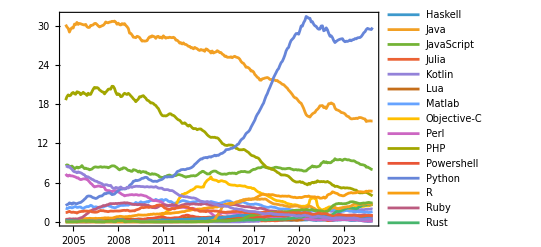

```mathematica
DateListPlot[rawDataset[10;;,All],PlotRange->{Automatic,All}]
```

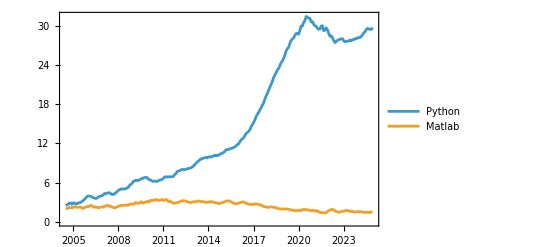

```mathematica
DateListPlot[rawDataset[{"Python","Matlab"}],PlotRange->{Automatic,All}]
```

## Organizing Files

## Using SetDirectory

One good way to organize your data files is to use the SetDirectory function. Once you have set the working directory, the Wolfram Language will automatically look in the selected directory, so all you will need is the name of the file to import it. FileNameJoin will construct a proper file path for the operating system you are using. If you keep your data file directory and notebooks in the same location, you can move your work from one machine to another, and everything will work with the same inputs.

See directory that your Notebook file is saved (Not the kernel’s current working directory.):

```mathematica
NotebookDirectory[]
```

/Users/murilo/Master_programs/UoA/DataScience/Lecturers/2023/

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"DataDir/Lec6"}]]
```

/Users/murilo/Master_programs/UoA/DataScience/Lecturers/2025-2026/DataDir/Lec6

Get the names of the files in the selected directory using FileNames.

```mathematica
FileNames[]
```

{Aircraft_Incident_Dataset.csv,Base_MUNIC_2021_MERGED.xlsx,Base_MUNIC_2021.xlsx,breamData.csv,chicagotemps.csv,Most Popular Programming Languages from 2004 to 2021.csv,RenewablesGrowth.xls,RenewablesGrowth.xlsx,stockdata.csv,table_1_14_a.xlsx,test1.xlsx,test.xlsx}

Choose the type of file you want to shorten the list.

```mathematica
FileNames["*.csv"]
```

{Aircraft_Incident_Dataset.csv,breamData.csv,chicagotemps.csv,Most Popular Programming Languages from 2004 to 2021.csv,stockdata.csv}

# Organizing Files

## Defining a Path

You can use FileNameJoin to create a path for your computer that you can use in defining a function to get files using only the file name. You may find a function ToFileName in some documentation examples, but you should use FileNameJoin. The older ToFileName has been replaced.

Define the path.

```mathematica
myPath= FileNameJoin[{NotebookDirectory[],"DataDir/Lec6"}]
```

/Users/murilo/Master_programs/UoA/DataScience/Lecturers/2025-2026/DataDir/Lec6

Define a function to get files.

```mathematica
getFile[nm_String]:= Import[FileNameJoin[{myPath,nm}]]
```

Notice that if you place // Short  as a Posfix function, then the variable “Chic” bellow will have Dimension = 1, meaning that all the data will be inside the single Row.

Use // Short to visualize data, but it is not a good practice if this data will be input in a variable.

```mathematica
Chic = getFile["chicagotemps.csv"];
```

```mathematica
Chic//Short
```

{{{2007, 1, 1},5.85},{{2007, 1, 7},2.69},«103»,{{2008, 12, 28},-0.63},{{2009, 1, 1},-5.43}}

```mathematica
Chic = Import["chicagotemps.csv"]//Short
```

{{{2007, 1, 1},5.85},{{2007, 1, 7},2.69},«103»,{{2008, 12, 28},-0.63},{{2009, 1, 1},-5.43}}

After Importing, always ensure to understand the structure behind the data:

```mathematica
Chic//Dimensions
```

{1}

```mathematica
Chic[[1]];
```

Bellow (without the Short) the full data dimensionality will be preserved.

```mathematica
Chic = Import["chicagotemps.csv"];
```

```mathematica
Dimensions[Chic]
```

{107,2}

The data is a list of elements, and it is already organized in the format appropriate to be plot as a timeseries with points: {time,value}

```mathematica
Chic//Dataset
```

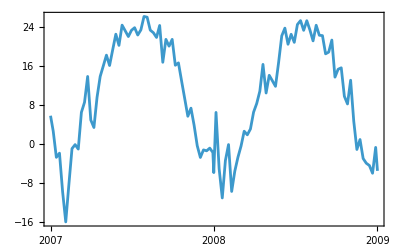

```mathematica
DateListPlot[%]
```

# Importing data: Excel-XLS

## Excel Files

Excel files consist of one or more sheets. With the default behaviour, the Wolfram Language will bring in all the sheets as a list of arrays. In the first example, an entire file is brought in, with the older extension XLS.

Check to make sure you are in the kernel’s current working directory.

```mathematica
Directory[]
```

/Users/murilo/Master_programs/UoA/DataScience/Lecturers/2025-2026/DataDir/Lec6

Find the names of the Excel files. The Wolfram Language supports both XLS and XLSX formats.

```mathematica
FileNames["*.xls"|"*.xlsx"]
```

{Base_MUNIC_2021_MERGED.xlsx,Base_MUNIC_2021.xlsx,RCLC1d.xls,RenewablesGrowth.xls,RenewablesGrowth.xlsx,table_1_14_a.xlsx,test12.xlsx,test1.xlsx,test.xlsx}

## Importing Data: Excel. Let us understand the option “Data”.

The command bellow imports the element “Data” from the Excel sheet 1 (number 1 after “Data”) taking only the first element (row) of the list. There are 15 elements (rows), each with dimension 3 (3 elements inside).

Let us understand the option "Data". It makes Import to import only the data that can be put in an Array of numbers or strings. Remember that array is a uniform object, therefore, it only imports the data that can be put in regular Tables. See the following example:

Now, play around with changing the sheet numbers with the test.xlsx file :

```mathematica
dataFull=Import["test.xlsx",{"Data",1}]
```

{{2000.,10.,,,,,},{2001.,11.,,,,,},{2002.,12.,,,,,},{2003.,13.,,,,,},{1004.,14.,,,,,},{,,,,,,},{,,,123.,,,},{,,,,,,},{,,,,,,},{,,,,,,},{,,,,,,},{,,,,,,},{,,,,1231.,,},{,,,,,,},{,,,,,,},{,,,,,,},{,,,,,,abavbvs},{,,,,,,},{,,,4000.,10.,,},{,,,4001.,11.,,},{,,,4002.,12.,,},{,,,4003.,13.,,}}

```mathematica
dataTest= Import["test.xlsx",{"Data",3}]
```

{{,,,,1.,123.},{,,,,2.,246.},{,,,,3.,369.},{,,,,4.,492.},{,,,,5.,615.}}

To Import the first 2 rows of sheet 1 :

```mathematica
dataTest= Import["test.xlsx",{"Data",1,{1,2}}]
```

{{2000.,10.,,,,,},{2001.,11.,,,,,}}

The first 2 rows, but only column 2, in sheet 1 :

```mathematica
dataTest= Import["test.xlsx",{"Data",1,{1,2},2}]
```

{10.,11.}

To import all “Data” and the list of sheets do: :

```mathematica
dataTest= Import["test1.xlsx",{{"Data", "Sheets"}}]
```

{{{{2000.,10.,,,,,},{2001.,11.,,,,,},{2002.,12.,,,,,},{2003.,13.,,,,,},{1004.,14.,,,,,},{,,,,,,},{,,,123.,,,},{,,,,,,},{,,,,,,},{,,,,,,},{,,,,,,},{,,,,,,},{,,,,1231.,,},{,,,,,,},{,,,,,,},{,,,,,,},{,,,,,,abavbvs},{,,,,,,},{,,,4000.,10.,,},{,,,4001.,11.,,},{,,,4002.,12.,,},{,,,4003.,13.,,}},{{3000.,10.},{3001.,11.},{3002.,12.},{3003.,13.},{3004.,14.}},{{,,,,1.,123.},{,,,,2.,246.},{,,,,3.,369.},{,,,,4.,492.},{,,,,5.,615.}},{{1.,3.},{3.,5.}}},{page1,page2,page3,Sheet1}}

To see the list of sheets :

```mathematica
Import["test1.xlsx",{"Sheets"}]
```

{page1,page2,page3,Sheet1}

And finally, to Import a specific "Sheet"

```mathematica
dataTest= Import["test1.xlsx",{"Data","Sheet1"}]
```

{{1.,3.},{3.,5.}}

## Checking the File

The Wolfram Language contains a function, TableView, that is very useful for looking at the form of smaller files. You can use it to investigate the data you have imported.

This gives an idea of the size of the file: 15 rows and three columns.

```mathematica
Dimensions[dataFull]
```

{22,7}

```mathematica
TableView[dataFull]
```

2000.10.2001.11.2002.12.2003.13.1004.14.123.1231.abavbvs4000.10.4001.11.4002.12.4003.13.

```mathematica
Clear[dataFull]
```

If we had not specified that we wanted sheet 1, then Wolfram imports all the information, including the sheet itself as another dimension :

# Let us do some pre-processing

```mathematica
dataOriginal= Import["table_1_14_a.xlsx"];
```

```mathematica
dataOriginal[[1]]//Dataset
```

```mathematica
Dimensions[dataOriginal]
```

{1,68,12}

We can Import only Sheet 1

```mathematica
data= Import["table_1_14_a.xlsx",{"Data",1}];
```

```mathematica
Dimensions[data]
```

{68,12}

The bellow now specifies a value in the cell (20, 3)

```mathematica
data[[20,3]]
```

325.

Basically, transforms the expr into something that Mathematica can understand.

The command bellow gets the first row from the data. Note that in InputForm there are a number of empty strings. These are placeholders for cells in the Excel document having no content. Also, we can see that Table.. is actually a string.

```mathematica
data[[1]]
```

{Table 1.14.A. Net Generation from Other Renewable Sources,,,,,,,,,,,}

```mathematica
data[[1]]//InputForm
```

{"Table 1.14.A. Net Generation from Other Renewable Sources", "", "", "", "", "", "", "", "", "", "", ""}

Compare with ToExpression

```mathematica
data[[1]]//ToExpression
```

{from Generation Other Renewable Sources Table 1.14.A.Net,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

Transforming a row list into a column:

```mathematica
Column[{data[[1]],"  ",data[[1]]//InputForm}]
```

{Table 1.14.A. Net Generation from Other Renewable Sources,,,,,,,,,,,}
  
{"Table 1.14.A. Net Generation from Other Renewable Sources", "", "", "", "", "", "", "", "", "", "", ""}

To delete the empty Strings do

```mathematica
data[[1]];
```

```mathematica
DeleteCases[data[[1]],""]
```

{Table 1.14.A. Net Generation from Other Renewable Sources}

Or, replace to something, and then delete it !

```mathematica
DeleteCases[data[[1]]/. ""->x,x]
```

{Table 1.14.A. Net Generation from Other Renewable Sources}

notice you can replace empty values:

```mathematica
Clear[x]
```

```mathematica
data[[1]]/. ""->x
```

{Table 1.14.A. Net Generation from Other Renewable Sources,x,x,x,x,x,x,x,x,x,x,x}

## Extracting by position and patterns

Here are the first four elements of the sixth row, together with the associated data types. While it may seem to be overkill to look at such things, many users overlook these details and then wonder why they do not get answers.

```mathematica
Grid[{data[[6,;;4]],Head/@data[[6,;;4]]}]
```

New England | 834. | 744. | 0.121
String | Real | Real | Real

This gets the positions in the array for the second element from the first eight rows which are numeric :

Bellow we are trying to discover when the numbers start appearing in the table

Bellow you can discover where are the numbers in column 2, in the first eight rows :

```mathematica
data[[;;8,2]]
```

{,,,All Sectors,January 2013,834.,53.,405.}

```mathematica
Position[data[[;;8,2]],_?NumericQ]
```

{{6},{7},{8}}

Specific data (numeric in this case) can be visualized after knowing the position :

```mathematica
data[[6;;8,2]]
```

{834.,53.,405.}

We can Flatten the list of list obtained from Position

```mathematica
a=Flatten[Position[data[[;;8,2]],_?NumericQ]]
```

{6,7,8}

To use in data to extract the first number :

```mathematica
data[[a[[1]],2]]
```

834.

or to get all the data for the positions previously selected :

```mathematica
data[[a,2]]
```

{834.,53.,405.}

You can use the Extract function together with the Position function to get the values that are numeric.

```mathematica
-Graphics--Graphics-
```

The numeric values for “All Sectors” are in the second column.

```mathematica
data[[;;8,2]]
```

{,,,All Sectors,January 2013,834.,53.,405.}

```mathematica
Position[data[[All,2]],_?NumericQ]
```

{{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},{50},{51},{52},{53},{54},{55},{56},{57},{58},{59},{60},{61},{62},{63},{64},{66},{67}}

Obtaining the numbers:

```mathematica
Extract[data[[All,2]],Position[data[[All,2]],_?NumericQ]]
```

{834.,53.,405.,157.,141.,10.,68.,1238.,88.,590.,559.,2634.,1203.,478.,419.,197.,338.,4516.,1665.,732.,973.,125.,156.,602.,263.,1515.,8.,398.,284.,82.,215.,154.,199.,175.,498.,269.,27.,113.,90.,3961.,149.,228.,850.,2734.,2377.,132.,658.,261.,204.,306.,208.,59.,551.,3493.,2273.,553.,666.,85.,77.,21152.}

Or from the data :

```mathematica
Flatten[Position[data[[All,2]],_?NumericQ]]
```

{6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,66,67}

You could also do :

```mathematica
data[[Flatten[Position[data[[All,2]],_?NumericQ]],2]]
```

{834.,53.,405.,157.,141.,10.,68.,1238.,88.,590.,559.,2634.,1203.,478.,419.,197.,338.,4516.,1665.,732.,973.,125.,156.,602.,263.,1515.,8.,398.,284.,82.,215.,154.,199.,175.,498.,269.,27.,113.,90.,3961.,149.,228.,850.,2734.,2377.,132.,658.,261.,204.,306.,208.,59.,551.,3493.,2273.,553.,666.,85.,77.,21152.}

Select elements that are larger than 100 :

```mathematica
Select[data[[All,2]],#>100&]
```

{834.,405.,157.,141.,1238.,590.,559.,2634.,1203.,478.,419.,197.,338.,4516.,1665.,732.,973.,125.,156.,602.,263.,1515.,398.,284.,215.,154.,199.,175.,498.,269.,113.,3961.,149.,228.,850.,2734.,2377.,132.,658.,261.,204.,306.,208.,551.,3493.,2273.,553.,666.,21152.}

# Extracting by Cases

A more direct way to extract!

## Cases

## Cases requires knowing something about level specifications in expressions, and elements not at the top level of an expression may not be found. -Graphics-

```mathematica
Cases[data[[All,2]],_?NumericQ]
```

{834.,53.,405.,157.,141.,10.,68.,1238.,88.,590.,559.,2634.,1203.,478.,419.,197.,338.,4516.,1665.,732.,973.,125.,156.,602.,263.,1515.,8.,398.,284.,82.,215.,154.,199.,175.,498.,269.,27.,113.,90.,3961.,149.,228.,850.,2734.,2377.,132.,658.,261.,204.,306.,208.,59.,551.,3493.,2273.,553.,666.,85.,77.,21152.}

To get values in the second and third columns, you need to specify up to what level you want the function Cases to consider. For example,

```mathematica
Clear[aa]
```

```mathematica
aa={1,{1,2},{1,{2,3}}}
```

{1,{1,2},{1,{2,3}}}

Extract up to the third level :

```mathematica
Cases[aa,_?NumericQ,3]
```

{1,1,2,1,2,3}

This extracts columns 2 and 3 of the dataset

```mathematica
data[[All,{2,3}]]//Shallow
```

{{,},{,},{,},{All Sectors,},{January 2013,January 2012},{834.,744.},{53.,56.},{405.,417.},{157.,104.},{141.,111.},«58»}

```mathematica
Cases[data[[All,{2,3}]],_?NumericQ,2]//Shallow
```

{834.,744.,53.,56.,405.,417.,157.,104.,141.,111.,«110»}

Note that Cases does not preserve the data structure if you do not specify the structure. It can be a dimensional reduction operation.

If you are more specific with what you want, Cases will give numerical ordered pairs and maintain the structure (list of list of 2 numbers)

```mathematica
Cases[data[[6;;,2;;3]],{_?NumericQ,_?NumericQ}]//Shallow
```

{{834.,744.},{53.,56.},{405.,417.},{157.,104.},{141.,111.},{10.,11.},{68.,46.},{1238.,1126.},{88.,87.},{590.,579.},«50»}

## A hands-on use of Position, PatternTest, Case to detect outlyer and replace its value

```mathematica
rawOilPrices=Import["http://www.eia.gov/dnav/pet/hist_xls/RCLC1d.xls"];
```

```mathematica
Dimensions[rawOilPrices]
```

{2}

```mathematica
Export["/Users/murilo/Master_programs/UoA/DataScience/Lecturers/2025-2026/DataDir/Lec6/RCLC1d.xls",rawOilPrices]
```

/Users/murilo/Master_programs/UoA/DataScience/Lecturers/2025/DataDir/Lec6/RCLC1d.xls

```mathematica
oilPrices=rawOilPrices[[2,All]];
```

If I want to Drop first 3 elements of data:

```mathematica
oilPrices
```

```mathematica
Drop[oilPrices,3]
```

That can be done all together with Cases function

```mathematica
cleanedOilPrices=Cases[oilPrices,{_,_?NumberQ}]
```

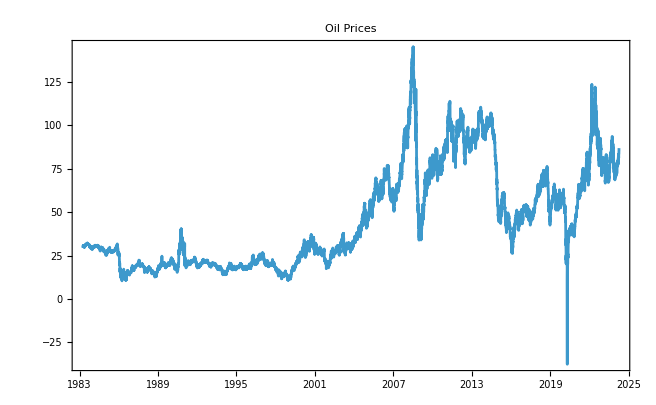

```mathematica
Show[DateListPlot[cleanedOilPrices,PlotLabel->"Oil Prices"],DateListPlot[{cleanedOilPrices[[9302]]},PlotStyle->{Thickness[0.05],Red}],PlotRange->All]
```

```mathematica
cleanedOilPrices[[9302]]
```

{Mon 20 Apr 2020 00:00:00GMT,-37.63}

```mathematica
Position[cleanedOilPrices[[All,2]],_?Negative]
```

{{9302}}

```mathematica
cleanedOilPrices[[All,2]];
```

or

```mathematica
Position[cleanedOilPrices[[All,2]],a_/;a<0 ]
```

{{9302}}

For this case, I would replace the value with the average between the previous and next day

```mathematica
cleanedOilPrices[[9302,2]]=(cleanedOilPrices[[9301,2]]+cleanedOilPrices[[9303,2]])/2
```

14.14

```mathematica
cleanedOilPrices[[9301;;9303,2]]
```

{18.27,14.14,10.01}

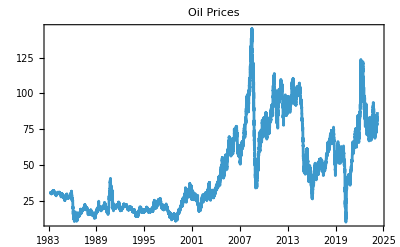

```mathematica
Show[DateListPlot[cleanedOilPrices,PlotLabel->"Oil Prices"],DateListPlot[{cleanedOilPrices[[9302]]},PlotStyle->{Thickness[0.05],Red}],PlotRange->All]
```

# Cleaning Up the Data

Import the stock data.

```mathematica
stkDat=Import["stockdata.csv","Table"]
```

{{Jul,3,2006,11228.02},{Jul,5,2006,11151.82},{Jul,6,2006,11225.3},{Jul,7,2006,11090.67},{Jul,10,2006,11103.55},{Jul,11,2006,11134.77},{Jul,12,2006,11013.18},{Jul,13,2006,10846.29},{Jul,14,2006,10739.35},{Jul,17,2006,10747.36},{Jul,18,2006,10799.23},{Jul,19,2006,11011.42},{Jul,20,2006,10928.1},{Jul,21,2006,10868.38},{Jul,24,2006,11051.05},{Jul,25,2006,11103.71},{Jul,26,2006,11102.51},{Jul,27,2006,11100.43},{Jul,28,2006,11219.7},{Jul,31,2006,11185.68},{Aug,1,2006,11125.73},{Aug,2,2006,11199.92},{Aug,3,2006,11242.59},{Aug,4,2006,11240.35},{Aug,7,2006,11219.38},{Aug,8,2006,11173.59},{Aug,9,2006,11076.18},{Aug,10,2006,11124.37},{Aug,11,2006,11088.02},{Aug,14,2006,11097.87},{Aug,15,2006,11230.26},{Aug,16,2006,11327.12},{Aug,17,2006,11334.96},{Aug,18,2006,11381.47},{Aug,21,2006,11345.04},{Aug,22,2006,11339.84},{Aug,23,2006,11297.9},{Aug,24,2006,11304.46},{Aug,25,2006,11284.05},{Aug,28,2006,11352.01},{Aug,29,2006,11369.94},{Aug,30,2006,11382.91},{Aug,31,2006,11381.15},{Sep,1,2006,11464.15},{Sep,5,2006,11469.28},{Sep,6,2006,11406.2},{Sep,7,2006,11331.44},{Sep,8,2006,11392.11},{Sep,11,2006,11396.84},{Sep,12,2006,11498.09},{Sep,13,2006,11543.32},{Sep,14,2006,11527.39},{Sep,15,2006,11560.77},{Sep,18,2006,11555.},{Sep,19,2006,11540.91},{Sep,20,2006,11613.19},{Sep,21,2006,11533.23},{Sep,22,2006,11508.1},{Sep,25,2006,11575.81},{Sep,26,2006,11669.39},{Sep,27,2006,11689.24},{Sep,28,2006,11718.45},{Sep,29,2006,11679.07}}

## Split and Replace

```mathematica
-Graphics--Graphics-
```

You can use some string manipulations to make things work. Break a string into usable parts using StringSplit. After breaking the string up, rearrange the terms in the expression and reassemble them in a usable form through repeated use of ReplaceAll.

Checking on the abbreviations used for the months.

```mathematica
stkDat[[All,1]]
```

{Jul,Jul,Jul,Jul,Jul,Jul,Jul,Jul,Jul,Jul,Jul,Jul,Jul,Jul,Jul,Jul,Jul,Jul,Jul,Jul,Aug,Aug,Aug,Aug,Aug,Aug,Aug,Aug,Aug,Aug,Aug,Aug,Aug,Aug,Aug,Aug,Aug,Aug,Aug,Aug,Aug,Aug,Aug,Sep,Sep,Sep,Sep,Sep,Sep,Sep,Sep,Sep,Sep,Sep,Sep,Sep,Sep,Sep,Sep,Sep,Sep,Sep,Sep}

```mathematica
DeleteDuplicates[stkDat[[All,1]]]
```

{Jul,Aug,Sep}

Experimenting with a single row of the data. Begin by splitting the year and value

Syntax:

expr /. rule— replace All using a rule ("slash dot"). You can also use the function ReplaceAll[rules]

```mathematica
?ReplaceAll
```

lhs:>rhs or lhs:>rhs : represents a rule that transforms lhs to rhs, evaluating rhs only after the rule is used.

The character :> can be entered as :> simply or ESC + :>+ ESC  or∖[RuleDelayed].

## See the difference :

```mathematica
{x,x,x}/. x->RandomReal[]
```

{0.592968,0.592968,0.592968}

All x are replaced in the left list by a random number, the same number, since RandomReal is evaluated when replacing the x to it .

```mathematica
{x,x,x}/. x:> RandomReal[]
```

{0.865375,0.689525,0.202786}

The list {x, x, x} is replaced with {RandomReal[], RandomReal[], RandomReal[]} and then evaluated .

## Back to our data cleaning

```mathematica
stkDat[[1]]
```

{Jul,3,2006,11228.02}

```mathematica
stkDat[[1]]//InputForm
```

{"Jul", 3, "2006,11228.02"}

Reason for the delay function ahead is to delay the replace all so that the list is not replaced before checking pattern

Bellow, ReplaceAll using  rule :

a_String is an input argument that is a String.  _String  matches any string, but not a symbol. Bellow checks for if there is a {String, Something, String}.

Notice that bellow creates a list:

```mathematica
StringSplit["2006,11228.02",","]
```

{2006,11228.02}

```mathematica
stkDat[[1,3]]
```

2006,11228.02

```mathematica
Head[stkDat[[1,3]]]
```

String

```mathematica
stkDat[[1]]
```

{Jul,3,2006,11228.02}

```mathematica
res=stkDat[[1]]/.{a_String,b_,c_String}:> {a,b,StringSplit[c,","]}
```

{Jul,3,{2006,11228.02}}

We can Flatten, do it to proceed :

```mathematica
res=Flatten[%]
```

{Jul,3,2006,11228.02}

This rule (after /.) I will call rules1

```mathematica
rules1={a_String,b_,c_String}:> Flatten[{a,b,StringSplit[c,","]}];
```

What we have done before but using these functions :

```mathematica
stkDat[[1]]/.rules1
```

{Jul,3,2006,11228.02}

```mathematica
stkDat[[1]]/.{a_String,b_,c_String}:> Flatten[{a,b,StringSplit[c,","]}]
```

{Jul,3,2006,11228.02}

ToExpression will attempt to interpret any string as Wolfram Language input, bellow it will transform a string of numbers into a number. (InputForm-> print suitable expression to input in Wolfram language, ToExpression interprets it as a Wolfram input)

```mathematica
Head["2345"]
```

String

```mathematica
ToExpression["2345"]
```

2345

```mathematica
Head[ToExpression["2345"]]
```

Integer

Remember:

```mathematica
res=stkDat[[1]]/.rules1
```

{Jul,3,2006,11228.02}

```mathematica
{"Jul",3,"2006","11228.02"}
```

We now create a rule to transform the data into a DateObject

```mathematica
rules2={a_,b_,c_,d_}:> {DateObject[{ToExpression[c],a/.{"Jul"-> 7,"Aug"-> 8,"Sep"-> 9},b}],ToExpression[d]}
```

{a_,b_,c_,d_}:>{DateObject[{ToExpression[c],a/.{Jul→7,Aug→8,Sep→9},b}],ToExpression[d]}

```mathematica
stkDat[[1]]/.rules1/.rules2
```

{Mon 3 Jul 2006,11228.}

```mathematica
lalala=TimeSeries[stkDat3=stkDat/.rules1/.rules2];
```

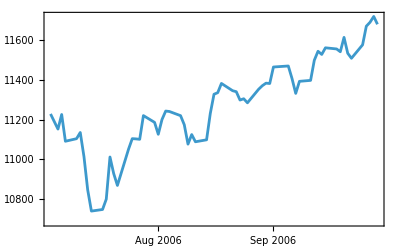

```mathematica
DateListPlot[lalala]
```

# Data Cleaning

## Replacing Missing or Incorrect Data

While this is certainly not an appropriate approach in all cases, there are situations where it is a reasonable thing to do. The file breamData.csv contains an example. This file contains a subset of data collected in Finland in the early twentieth century. Begin by bringing the data into the Wolfram Language and formatting it using TableView.

```mathematica
FileNames["*.csv"]
```

{Aircraft_Incident_Dataset.csv,breamData.csv,chicagotemps.csv,Most Popular Programming Languages from 2004 to 2021.csv,stockdata.csv}

The breamData.csv file consists of information about 159 fish taken from Lake Laengelmavesi, Finland. The data included seven species, and this file contains the information on one of the most frequent species.

```mathematica
breamDat= Import["breamData.csv",{"Data"}]
```

{{1,242.,23.2,25.4,30.,38.4,13.4},{1,290.,24.,26.3,31.2,40.,13.8},{1,340.,23.9,26.5,31.1,39.8,15.1},{1,363.,26.3,29.,33.5,38.,13.3},{1,430.,26.5,29.,34.,36.6,15.1},{1,450.,26.8,29.7,34.7,39.2,14.2},{1,500.,26.8,29.7,34.5,41.1,15.3},{1,390.,27.6,30.,35.,36.2,13.4},{1,450.,27.6,30.,35.1,39.9,13.8},{1,500.,28.5,30.7,36.2,39.3,13.7},{1,475.,28.4,31.,36.2,39.4,14.1},{1,500.,28.7,31.,36.2,39.7,13.3},{1,500.,29.1,31.5,36.4,37.8,12.},{1,Missing[NotAvailable],29.5,32.,37.3,37.3,13.6},{1,600.,29.4,32.,37.2,40.2,13.9},{1,600.,29.4,32.,37.2,41.5,15.},{1,700.,30.4,33.,38.3,38.8,13.8},{1,700.,30.4,33.,38.5,38.8,13.5},{1,610.,30.9,33.5,38.6,40.5,13.3},{1,650.,31.,33.5,38.7,37.4,14.8},{1,575.,31.3,34.,39.5,38.3,14.1},{1,685.,31.4,34.,39.2,40.8,13.7},{1,620.,31.5,34.5,39.7,39.1,13.3},{1,680.,31.8,35.,40.6,38.1,15.1},{1,700.,31.9,35.,40.5,40.1,13.8},{1,725.,31.8,35.,40.9,40.,14.8},{1,720.,32.,35.,40.6,40.3,15.},{1,714.,32.7,36.,41.5,39.8,14.1},{1,850.,32.8,36.,41.6,40.6,14.9},{1,1000.,33.5,37.,42.6,44.5,15.5},{1,920.,35.,38.5,44.1,40.9,14.3},{1,955.,35.,38.5,44.,41.1,14.3},{1,925.,36.2,39.5,45.3,41.4,14.9},{1,975.,37.4,41.,45.9,40.6,14.7},{1,950.,38.,41.,46.5,37.9,13.7},{The column headings are species, weight, length 1, length 2, length 3, height, thickness}}

Notice the Missing[NotAvailable] as Import from a csv file. I will replace to “NA”, as TableView has issues with Missing[]

```mathematica
breamDat=Replace[breamDat,Missing["NotAvailable"]-> "NA",2]
```

{{1,242.,23.2,25.4,30.,38.4,13.4},{1,290.,24.,26.3,31.2,40.,13.8},{1,340.,23.9,26.5,31.1,39.8,15.1},{1,363.,26.3,29.,33.5,38.,13.3},{1,430.,26.5,29.,34.,36.6,15.1},{1,450.,26.8,29.7,34.7,39.2,14.2},{1,500.,26.8,29.7,34.5,41.1,15.3},{1,390.,27.6,30.,35.,36.2,13.4},{1,450.,27.6,30.,35.1,39.9,13.8},{1,500.,28.5,30.7,36.2,39.3,13.7},{1,475.,28.4,31.,36.2,39.4,14.1},{1,500.,28.7,31.,36.2,39.7,13.3},{1,500.,29.1,31.5,36.4,37.8,12.},{1,NA,29.5,32.,37.3,37.3,13.6},{1,600.,29.4,32.,37.2,40.2,13.9},{1,600.,29.4,32.,37.2,41.5,15.},{1,700.,30.4,33.,38.3,38.8,13.8},{1,700.,30.4,33.,38.5,38.8,13.5},{1,610.,30.9,33.5,38.6,40.5,13.3},{1,650.,31.,33.5,38.7,37.4,14.8},{1,575.,31.3,34.,39.5,38.3,14.1},{1,685.,31.4,34.,39.2,40.8,13.7},{1,620.,31.5,34.5,39.7,39.1,13.3},{1,680.,31.8,35.,40.6,38.1,15.1},{1,700.,31.9,35.,40.5,40.1,13.8},{1,725.,31.8,35.,40.9,40.,14.8},{1,720.,32.,35.,40.6,40.3,15.},{1,714.,32.7,36.,41.5,39.8,14.1},{1,850.,32.8,36.,41.6,40.6,14.9},{1,1000.,33.5,37.,42.6,44.5,15.5},{1,920.,35.,38.5,44.1,40.9,14.3},{1,955.,35.,38.5,44.,41.1,14.3},{1,925.,36.2,39.5,45.3,41.4,14.9},{1,975.,37.4,41.,45.9,40.6,14.7},{1,950.,38.,41.,46.5,37.9,13.7},{The column headings are species, weight, length 1, length 2, length 3, height, thickness}}

```mathematica
TableView[breamDat[[All,All]]]
```

1242.23.225.430.38.413.41290.24.26.331.240.13.81340.23.926.531.139.815.11363.26.329.33.538.13.31430.26.529.34.36.615.11450.26.829.734.739.214.21500.26.829.734.541.115.31390.27.630.35.36.213.41450.27.630.35.139.913.81500.28.530.736.239.313.71475.28.431.36.239.414.11500.28.731.36.239.713.31500.29.131.536.437.812.1NA29.532.37.337.313.61600.29.432.37.240.213.91600.29.432.37.241.515.1700.30.433.38.338.813.81700.30.433.38.538.813.51610.30.933.538.640.513.31650.31.33.538.737.414.81575.31.334.39.538.314.11685.31.434.39.240.813.71620.31.534.539.739.113.31680.31.835.40.638.115.11700.31.935.40.540.113.81725.31.835.40.940.14.81720.32.35.40.640.315.1714.32.736.41.539.814.11850.32.836.41.640.614.911000.33.537.42.644.515.51920.35.38.544.140.914.31955.35.38.544.41.114.31925.36.239.545.341.414.91975.37.441.45.940.614.71950.38.41.46.537.913.7The column headings are species, weight, length 1, length 2, length 3, height, thickness

The first thing you notice is that the first column consists entirely of ones. You can also see there is an NA in the second column. Also, the last row does not seem to be consistent with the others.

```mathematica
Dimensions[breamDat]
```

{36}

```mathematica
breamDat[[-1]]
```

{The column headings are species, weight, length 1, length 2, length 3, height, thickness}

Get rid of the first column and last row and check the dimensions of the resulting set.

```mathematica
breamDat2= breamDat[[;;-2,2;;]];
```

```mathematica
{rows,cols}=Dimensions[breamDat2]
```

{35,6}

# Cleaning Up the Data

## Finding the “bad values”, NA

Get information about the NA seen in the file. It will either be a symbol or a string. Note how the Wolfram Language allows you to get several pieces of information at once.

Location and data type of the offending entry.

Find the position where NA or “NA”  (NA | “NA”) appears

```mathematica
a=Flatten[Position[breamDat2,NA|"NA"]]
```

{14,1}

```mathematica
breamDat2[[a[[1]],a[[2]]]]
```

NA

or if you knew the column were the NA would be :

```mathematica
Position[breamDat2,{a_,b_,c_,d_,e_,f_}/;a=="NA"]
```

{{14}}

or you can use a more symbolic way to locate and understand where NA is using the function Extract and a list (a function) with the syntax “function”[#]&/@ “set”, “function is a function (bellow a list), “#” the argument, and “set” a dataset.

First we can Extract a value, but keeping the position where it appears

```mathematica
Extract[breamDat2,pos=Position[breamDat2,NA|"NA"]]
```

{NA}

Then, we construct a List containing information about the bad value

```mathematica
{pos,#,Head[#]}&/@Extract[breamDat2,pos=Position[breamDat2,NA|"NA"]]
```

{{{{14,1}},NA,String}}

```mathematica
TableView[breamDat2]
```

242.23.225.430.38.413.4290.24.26.331.240.13.8340.23.926.531.139.815.1363.26.329.33.538.13.3430.26.529.34.36.615.1450.26.829.734.739.214.2500.26.829.734.541.115.3390.27.630.35.36.213.4450.27.630.35.139.913.8500.28.530.736.239.313.7475.28.431.36.239.414.1500.28.731.36.239.713.3500.29.131.536.437.812.NA29.532.37.337.313.6600.29.432.37.240.213.9600.29.432.37.241.515.700.30.433.38.338.813.8700.30.433.38.538.813.5610.30.933.538.640.513.3650.31.33.538.737.414.8575.31.334.39.538.314.1685.31.434.39.240.813.7620.31.534.539.739.113.3680.31.835.40.638.115.1700.31.935.40.540.113.8725.31.835.40.940.14.8720.32.35.40.640.315.714.32.736.41.539.814.1850.32.836.41.640.614.91000.33.537.42.644.515.5920.35.38.544.140.914.3955.35.38.544.41.114.3925.36.239.545.341.414.9975.37.441.45.940.614.7950.38.41.46.537.913.7

# Cleaning Up the Data

## Determining a Replacement Value

The column headings of the original file were as follows.

```mathematica
breamDat[[-1]]
```

{The column headings are species, weight, length 1, length 2, length 3, height, thickness}

We have eliminated the first column, so we only have  “weight, length 1, length 2, length 3, height, thickness”. NA is in columns for Weight.

To reconstruct it an usual good idea is to estimate the unknown weight by calculating an average value of the density (<weight/length 3>) and then multiplying by the specific value of the length 3 for that species.

Get the information from the first and fourth columns, and delete the row with the missing value, so the whole columns will not participate.

```mathematica
fullRows=Delete[breamDat2[[All,{1,4}]],14]
```

{{242.,30.},{290.,31.2},{340.,31.1},{363.,33.5},{430.,34.},{450.,34.7},{500.,34.5},{390.,35.},{450.,35.1},{500.,36.2},{475.,36.2},{500.,36.2},{500.,36.4},{600.,37.2},{600.,37.2},{700.,38.3},{700.,38.5},{610.,38.6},{650.,38.7},{575.,39.5},{685.,39.2},{620.,39.7},{680.,40.6},{700.,40.5},{725.,40.9},{720.,40.6},{714.,41.5},{850.,41.6},{1000.,42.6},{920.,44.1},{955.,44.},{925.,45.3},{975.,45.9},{950.,46.5}}

```mathematica
mn=Mean[fullRows[[All,1]]/fullRows[[All,2]]]
```

15.9385

```mathematica
fullRows[[All,1]]/fullRows[[All,2]]
```

{8.06667,9.29487,10.9325,10.8358,12.6471,12.9683,14.4928,11.1429,12.8205,13.8122,13.1215,13.8122,13.7363,16.129,16.129,18.2768,18.1818,15.8031,16.7959,14.557,17.4745,15.6171,16.7488,17.284,17.7262,17.734,17.2048,20.4327,23.4742,20.8617,21.7045,20.4194,21.2418,20.4301}

Let us calculate length3*density, where density =<weight/length 3 >

```mathematica
mn breamDat2[[14,4]]
```

594.507

```mathematica
Round[mn breamDat2[[14,4]]]
```

595

Replace the NA in the fourteenth row with the scaled value of L3 in that row (basically <weight/length 3> *length 3 ).

```mathematica
breamDat2[[14,1]]=N@Round[mn breamDat2[[14,4]]]
```

595.

```mathematica
TableView[breamDat2]
```

1:eJyFlD9LXEEUxR8WVha22xkCIokmhYXGfzvvvcnaWIidnQQiVgqKQYLBjX+2
kDWxVD+AWC7sF/ADaG86qyW9Tcqs7/xmHjNPcODxmDtnzpx77p1582Vr5etA
kiRv+99gwjCbZrIYU2a9GJ+MFhaI5+b+7nm8U3xkm/VpxZdmwNWJW3N1+Tze
a252xdub0rw5o/VanXjO/g9a73zzvOKb1//WMM/hR8/jd88b4JMUnizkH9kn
H3R358W3msKb48M4+g8qeMXhb7t84V/bYz7rfZQ++GtZ5Od+BS/eVOc95ZGf
B/DNoWfB8xayr51+8J0fzOfgr3u89jv/y3wVr+KL/5/I/z5e6/jSrMOHnl4G
z5j+F4fgXJ0MujP/13703x6iv8TrfPTULH6+jte6JU69Hk/AuzqhZ9T5GPn/
Al7HlHjxgx8+wgfw/T5WX4IzNvRz+dj77vDqT+rUJe/LCa3/+wmfu38p+3Kf
R1DfDae/xId9b8P+WTvydZXe1PeB+jTuhxPqAb7p7iF1Goruu/OzV+KdL8JH
78lNq8Jf0O24utrQn2aLuKnokT9RPyy38Nu9Nxl+2ui9ws/zU/wq8dJnw7zv
0GN++7pKD/ilz6w34PkIrh35gu9DDZ+38kXPw1kFL75G9F6B/9v291vn0QfX
8Hcj/Xu/fB/qHMs71Qh9XQffQU+Se7x0LbIv8/32H5mv5/Y=

We could have used Select to get the values in weights without the "NA"

```mathematica
Select[breamDat2[[All,1]],#!= "NA"&]
```

{242.,290.,340.,363.,430.,450.,500.,390.,450.,500.,475.,500.,500.,600.,600.,700.,700.,610.,650.,575.,685.,620.,680.,700.,725.,720.,714.,850.,1000.,920.,955.,925.,975.,950.}

## Extracting data from aircraft accidents, and using Cases followed by Counts to count types and # of events, and visualizing

Aircraft Accidents, Failures & Hijacks Dataset
A complete dataset of Aircraft Accidents, Failures & Hijacks since 1919 and up to 2022 [Link]

```mathematica
rawData=Import["/Users/murilo/Master_programs/UoA/DataScience/Lecturers/2025-2026/DataDir/Lec6/Aircraft_Incident_Dataset.csv"]
```

```mathematica
Dimensions[rawData]
```

{23519,23}

```mathematica
rawData[[1]]
```

{03-JAN-2022,British Aerospace 4121 Jetstream 41,ZS-NRJ,SA Airlink,Domestic Non Scheduled Passenger,Accident | repairable-damage,Airplane - Engines, Airplane - Engines - Prop/turbine blade separation, Collision - Object, Collision - Object - Bird, Result - Emergency, forced landing - On runway,near Venetia Mine...,Substantial,Monday 3 January 2022,08:10,03-JAN-2022,2 Garrett TPE331-14GR-805H,Fatalities: 0 / Occupants: 3,Fatalities: 0 / Occupants: 4,Fatalities: 0 / Occupants: 7,0,1995-05-19  (26 years 8 months),Landing (LDG),Johannesburg-O.R. Tambo International Airport (JNB/FAOR) , South Africa,Venetia Mine Airport (FAVM) , South Africa,Missing[NotAvailable],Missing[NotAvailable]}

```mathematica
rawData[[1,16]]
```

Fatalities: 0 / Occupants: 7

```mathematica
(*Extract just the data related with Domestic Scheduled Passenger flights, no fatalities (b=0)*)
scheduledPassengerRawData = Cases[rawData,{_,_,_,_,a_,_,_,_,_,_,_,_,_,_,_,_,b_,___}/;a=="Domestic Scheduled Passenger" && b==0];
scheduledPassengerRawData//Dimensions
```

{2249,23}

```mathematica
(*Extract just the data related with Domestic Scheduled Passenger flights and fatalities*)
scheduledPassengerRawDataFatalities = Cases[rawData,{_,_,_,_,a_,_,_,_,_,_,_,_,_,_,_,_,b_,___}/;a=="Domestic Scheduled Passenger" && b>0];
scheduledPassengerRawDataFatalities//Dimensions
```

{1755,23}

There were 1755 Domestic Flights accidents. Let us count the number for each type:

```mathematica
scheduledPassengerRawDataFatalities[[1;;10,7]]
```

{Result - Loss of control,Result - CFIT - Hill, mountain,Result - CFIT - Hill, mountain,Result - Runway excursion,Airplane - Engines, Airplane - Engines - All engine powerloss, Result - Loss of control,Result - Hijacking - Plane stormed, Security - Hijack,Airplane - Systems, Airplane - Systems - Electrical system, Landing/takeoff - Landing, Landing/takeoff - Landing - Bounced, Result - Emergency, forced landing - On runway,Result - Runway excursion,Airplane - Undercarriage, Airplane - Undercarriage - Brakes, Maintenance - Wrong installation of parts, Result - Runway excursion,Result - Loss of control}

```mathematica
(*Extract just the data related with incident cause (Column 7) when the accidents have fatalities, and count them, creating an association*)
```

```mathematica
allCausesFatalities=scheduledPassengerRawDataFatalities[[All,7]]//Counts;
```

```mathematica
allCausesFatalities;
```

```mathematica
(*Show by pie chart the more frequent causes of fatal accidents*)
```

```mathematica
PieChart[Take[ReverseSort[allCausesFatalities],5],ChartLegends->Automatic,ChartStyle-> "Rainbow"]
```

-Graphics-

What about the aircraft models that are most secure for accidents with fatalities (smaller number of accidents with fatalities)

```mathematica
allAircraftModelFatalities=scheduledPassengerRawDataFatalities[[All,2]]//Counts;
```

```mathematica
PieChart[Take[Sort[allAircraftModelFatalities],10],ChartLegends->Automatic,ChartStyle-> "Rainbow"]
```

-Graphics-

Most insecure (larger number of accidents with fatalities)

```mathematica
PieChart[Take[ReverseSort[allAircraftModelFatalities],10],ChartLegends->Automatic,ChartStyle-> "Rainbow"]
```

-Graphics-

Look for other companies

```mathematica
PieChart[Sort[allAircraftModelFatalities][[500;;510]],ChartLegends->Automatic,ChartStyle-> "Rainbow"]
```

-Graphics-

What about all aircraft model that had only 1 fatal accident?

```mathematica
Select[allAircraftModelFatalities,#==1&]//Dataset
```

# Upgrading to Dataset : List to Dataset

```mathematica
breamDat;
```

1) Join Keys with their values using the association format of the data

```mathematica
breamDat3 = Table[AssociationThread[{"species","weight","length1","length2", "length3", "height", "thickness"}-> breamDat[[i]]],{i,35}];
```

2) transform to a Dataset structure

```mathematica
breamDat4=Dataset[breamDat3]
```

We could have also used the bellow to create the association, which can then be converted to Dataset:

```mathematica
breamDat3=AssociationThread[ToString/@{"species","weight","length1","length2", "length3", "height", "thickness"}->#]&/@breamDat[[1;;35]];
```

# Replacing with Dataset

Extract a column of the Dataset :

```mathematica
breamDat4[All,"weight"]
```

Extracting a set of rows using Query :

```mathematica
Query[1;;2] @breamDat4
```

Missing[PartInvalid,1;;2]

Get the data for weight and length 3 excluding rows whose weights is larger than 10^4 (just to play around), using Select

You can extract only the list of particular weights using :

```mathematica
onlyWeight=breamDat4[Select[#weight<10^4&],"weight"]//Normal
```

{242.,290.,340.,363.,430.,450.,500.,390.,450.,500.,475.,500.,500.,600.,600.,700.,700.,610.,650.,575.,685.,620.,680.,700.,725.,720.,714.,850.,1000.,920.,955.,925.,975.,950.}

Extract the length3 for which the weight is larger than ...

```mathematica
onlyLength=breamDat4[Select[#weight<10^4&],"length3"]//Normal
```

{30.,31.2,31.1,33.5,34.,34.7,34.5,35.,35.1,36.2,36.2,36.2,36.4,37.2,37.2,38.3,38.5,38.6,38.7,39.5,39.2,39.7,40.6,40.5,40.9,40.6,41.5,41.6,42.6,44.1,44.,45.3,45.9,46.5}

```mathematica
media = Mean[onlyWeight/onlyLength]
```

15.9385

or you could simply ask for NOT( ! = ) “NA”

```mathematica
onlyLength=breamDat4[Select[#weight!="NA"&],"length3"]//Normal
```

{30.,31.2,31.1,33.5,34.,34.7,34.5,35.,35.1,36.2,36.2,36.2,36.4,37.2,37.2,38.3,38.5,38.6,38.7,39.5,39.2,39.7,40.6,40.5,40.9,40.6,41.5,41.6,42.6,44.1,44.,45.3,45.9,46.5}

Correct the NA data, by doing a Query....

You cannot simply add a value at a given cell of a Dataset. You need to use a Query function, or some other operation allowed to the Dataset

```mathematica
Query[All,Association[#,"weight"->If[#weight=="NA" ,#length3 media ,#weight]]&][breamDat4];
```

Notice that you do not need to know the location of the NA

Then, you need to store the values of the updated Dataset:

```mathematica
breamDat4 = Query[All,Association[#,"weight"->If[#weight=="NA" ,#length3 media ,#weight]]&][breamDat4]
```

```mathematica
breamDat4[3,4]=3;
```

Set::write: Tag Dataset in … is Protected.

## Useful “Downgrading” transformation to pre-processing

## Datasets to Associations

We can transform the Dataset to an Association simply doing :

```mathematica
backToasso=Normal[breamDat4];
```

## Useful "Downgrading" transformation to pre - processing.

## Association to List: 2 ways to do it

## First way :

```mathematica
asso=<|data1->{1,2,3,4},data2->{5,4,3,2},data3->{5,7,3,4}|>
```

<|data1→{1,2,3,4},data2→{5,4,3,2},data3→{5,7,3,4}|>

```mathematica
Clear[data1]
```

```mathematica
Dataset[asso]
```

```mathematica
Normal[asso]
```

{data1→{1,2,3,4},data2→{5,4,3,2},data3→{5,7,3,4}}

```mathematica
{data1->{1,2,3,4},data2->{5,4,3,2},data3->{5,7,3,4}}
```

Do :

```mathematica
MapApply[List,Normal[asso]]
```

{{data1,{1,2,3,4}},{data2,{5,4,3,2}},{data3,{5,7,3,4}}}

Notice that :

```mathematica
MapApply[List,{data1->{1,2,3,4}}]
```

simply makes Rule[data1, {1, 2, 3, 4}]  to become List[data1, {1, 2, 3, 4}]

{{data1,{1,2,3,4}}}

or

```mathematica
List@@@Normal[asso]
```

or

## Second way

So, it places the keys inside the list.

```mathematica
KeyValueMap[{##}&]@asso
```

{{data1,{1,2,3,4}},{data2,{5,4,3,2}},{data3,{5,7,3,4}}}

```mathematica
KeyValueMap[Flatten[{##}]&]@asso;
```

```mathematica
{{data1,1,2,3,4},{data2,5,4,3,2},{data3,5,7,3,4}}//Transpose//MatrixForm
```

(data1 | data2 | data3
1 | 5 | 5
2 | 4 | 7
3 | 3 | 3
4 | 2 | 4)

## Third way :

You can combine matrices column - wise with Join[mat1, mat2, 2]

```mathematica
Keys[asso]
```

{data1,data2,data3}

```mathematica
Transpose[{Keys[asso]}]//MatrixForm
```

(data1
data2
data3)

```mathematica
Values[asso]
```

{{1,2,3,4},{5,4,3,2},{5,7,3,4}}

```mathematica
{{1,2,3,4},{5,4,3,2},{5,7,3,4}}//MatrixForm
```

(1 | 2 | 3 | 4
5 | 4 | 3 | 2
5 | 7 | 3 | 4)

```mathematica
asso=<|data1->{1,2,3,4},data2->{5,4,3,2},data3->{5,7,3,4}|>;
Join[Transpose[{Keys[asso]}],Values[asso],2]//MatrixForm
```

(data1 | 1 | 2 | 3 | 4
data2 | 5 | 4 | 3 | 2
data3 | 5 | 7 | 3 | 4)

Let us see "inside" the Join level 2

```mathematica
Transpose[{Keys[asso]}]
```

{{data1},{data2},{data3}}

```mathematica
Values[asso]
```

{{1,2,3,4},{5,4,3,2},{5,7,3,4}}

```mathematica
Join[Transpose[{Keys[asso]}],Values[asso],2]
```

{{data1,1,2,3,4},{data2,5,4,3,2},{data3,5,7,3,4}}

```mathematica
Join[Transpose[{Keys[asso]}],Values[asso],2]//Transpose//MatrixForm
```

(data1 | data2 | data3
1 | 5 | 5
2 | 4 | 7
3 | 3 | 3
4 | 2 | 4)

## Integrating datasets with Dataset (and associations)

This topic was already covered, I left here just for completeness of this class .

Following stackexchange

```mathematica
ds=Dataset[{<|"char"->1,"freq"->0.1|>,<|"char"->2,"freq"->0.2|>,<|"char"->3,"freq"->0.3|>,<|"char"->0,"freq"->0.4|>}]
```

New dataset to be added as a new column:

```mathematica
intervals={{0,0.4},{0.4,0.7},{0.7,0.9},{0.9,1.}};
intervals//MatrixForm
```

(0 | 0.4
0.4 | 0.7
0.7 | 0.9
0.9 | 1.)

```mathematica
ds//Transpose
```

```mathematica
ds//Transpose//Append["intervals"->intervals]
```

```mathematica
ds//Transpose//Append["intervals"->intervals]//Transpose
```

For other ways and also integrating associations, see  stackexchange

Moreover, for extra computing power of datasets, see  Stackexchange

# Download Data from the Built-in Wolfram Data Repository

2007 : CountryData, CityData, ElementData, etc. introduced in the Wolfram Language

2009: Wolfram/Alpha launches

2010: WolframAlpha function introduced in the Wolfram Language

2012: Quantity introduced in the Wolfram Language

2014: EntityValue, DateObject, TimeSeries, GeoGraphics introduced in the Wolfram Language

2017: Wolfram Data Repository launches (See the excellent Wolfram Blog)

Find a Data Resource :

using a browser and accessing the Wolfram Data Repository

or using the ResourceSearch function

Retrieve the data :

Using ResourceData function

Search the database :

```mathematica
ResourceSearchpaclet:ref/ResourceSearch[form] 
gives a dataset of resources that contain text matching form.
```

Each entry in the Wolfram Data Repository has an associated webpage, which describes the data it contains

```mathematica
ResourceSearch["poem"]
```

```mathematica
ResourceSearch["poem"][7]
```

Retrieve information about landing of meteorites :

```mathematica
ResourceSearch["astronomy"]
```

```mathematica
data = ResourceData["Meteorite Landings"]
```

Dataset[<>]

Extract Information of first 2 rows :

```mathematica
Query[1;;2]@data
```

or:

```mathematica
data[[1;;2]]
```

or for the Names only:

```mathematica
data[[All, "Name"]];
```

```mathematica
(*To plot in a map, but it is taking TOO long....*)
```

```mathematica
cityEntities=Interpreter["City"]/@DeleteDuplicates[data[[All, "Name"]]]
```

```mathematica
GeoListPlot[cityEntities,PlotStyle->Red,PlotMarkers->{Point,20}]
```

```mathematica
(* -------    *)
```

Use a list of terms that must all be included :

```mathematica
ResourceSearch[{"Network","Boston","Political"}]
```

Download an Entity Store:

```mathematica
ResourceData["Entity Store of Books in Stephen Wolfram's Library"]
```

EntityStore[<1>]

It describes a single entity type : an "SWLibraryBook".

To be able to use entities of this type just like built - in entities, we "register" the entity store :

```mathematica
EntityRegister[%]
```

{SWLibraryBook}

show data from one Entity

```mathematica
EntityClassList["SWLibraryBook"]
```

{Books with identifiers,Books without identifiers}

```mathematica
Entity["SWLibraryBook"]["Properties"]
```

{authors,ISBN,label,OpenLibrary ID,countries of publication,cities of publication,publisher,title,year of publication}

# Astronomical data using Entity

```mathematica
ClearAll["Global`*"]
```

Retrieving and plotting the Mass against the Radius of all known Exoplanets. First Querying the possible properties of Exoplanet:

```mathematica
EntityProperties["Exoplanet"];
```

```mathematica
rm=LinguisticAssistant
```

exoplanets

```mathematica
exoplanets = EntityValue[rm,{"Radius","Mass"}]
```

Several average radius are missing. To plot such data we can only consider the planets whose mass and radius are known. We can use the function DeleteMissing:

Consider the following created List. The fourth element has a missing at level 2 and the 5th a missing at level 3:

```mathematica
Clear[a]
```

```mathematica
data={Missing[], {a,1},{b,2},{c,Missing[]},{d,{Missing[]}}};
```

```mathematica
Head[{Missing[]}]
```

List

```mathematica
Head[Missing[]]
```

Missing

appliesDeleteMissingpaclet:ref/DeleteMissingto any lists or associations that occur within the first 1 levels ofexpr:

```mathematica
DeleteMissing[data,1]
```

{{a,1},{b,2},{c,Missing[]},{d,{Missing[]}}}

Notice that empty string is not Missing[] . Missing[] is curated data, returned from data functions like CountryData

appliesDeleteMissingpaclet:ref/DeleteMissingto any lists or associations that occur within the first 2 levels ofexpr:

```mathematica
DeleteMissing[data,1,2]
```

{{a,1},{b,2}}

Now, consider element at level n=1 missing if Missing occurs within the first d=Infinity levels of the element. In {h,{a},{b},{{c},d}}, h is in level 1, {a} is in level 1,{c} is in level 2.

```mathematica
DeleteMissing[data,1,Infinity]
```

{{a,1},{b,2}}

In data, {c, Missing[]} is an element at level 1. So, if there is any Missing[] inside at any level, the element {c, Missing[]} will be deleted.

In our data, all elements Missing[], {a,2}, {b,2}, {c,Missing[]}, {d,Missing[]}, {d,{Missing[]}} are at level 1. So, if we do DeleteMissing[data,1,Infinity] every sub-list at level 1 will be deleted if there is at any level a Missing[].

```mathematica
data
```

{Missing[],{a,1},{b,2},{c,Missing[]},{d,{Missing[]}}}

```mathematica
exoplanets[1;;10];
```

```mathematica
exoplanets = DeleteMissing[exoplanets,1,2];
```

```mathematica
exoplanets[1;;10];
```

```mathematica
ListPlot[exoplanets,Sequence[Frame->True,FrameLabel->{"radius (m)","mass (kg)"},ScalingFunctions->{"Log",None},PlotLabel->"Exoplanets Radius x Mass",PlotRange->{Automatic,{10^25,Automatic}},PlotMarkers->{Automatic,5},IntervalMarkersStyle->LightGray]]
```

-Graphics-

# Country Data

CountryData[] or CountryData[All] gives the list of all ordinary countries and dependencies.

CountryData[“Properties”] gives a list of all properties available for countries.

Querying the properties of the UK entity:

```mathematica
CountryData["UK","Properties"];
```

# Extracting and plotting the Countries Population against GDP, with label.

List of Entities for the countries in the world (not their names)

```mathematica
CountryData["Countries"];
```

The bellow extracts the names of the entities

```mathematica
CountryData[#,"Name"]&/@CountryData["Countries"];
```

-Graphics-

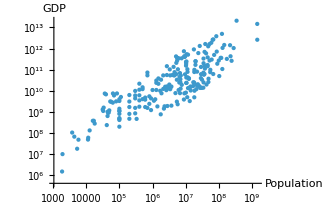

```mathematica
ListLogLogPlot[Tooltip[{CountryData[#,"Population"],CountryData[#,"GDP"]},CountryData[#,"Name"]]&/@CountryData["Countries"],AxesLabel->{"Population","GDP"}]
```

Above Tooltip[] labels points by CountryData[#, "Name"]

For the specific year of 2016 :

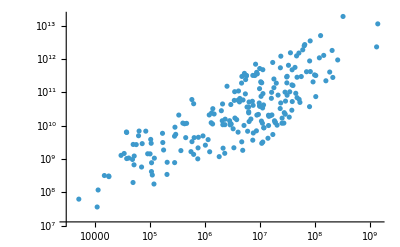

```mathematica
ListLogLogPlot[{CountryData[#,{{"Population"},2016}],CountryData[#,{{"GDP"},2016}]}&/@CountryData["Countries"]]
```

# GDP for varying time

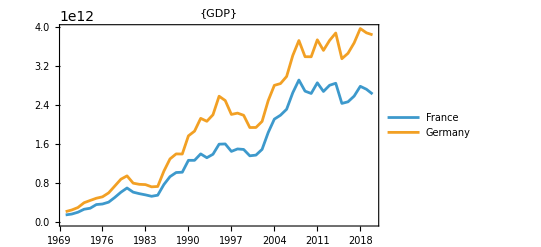

```mathematica
DateListPlot[{CountryData["France",{{"GDP"},{1970,2022}}],CountryData["Germany",{{"GDP"},{1970,2022}}]},PlotLegends->{"France","Germany"},PlotLabel->{"GDP"}]
```

# Selected list of ranked CountryData by area

```mathematica
CountryData[];
```

```mathematica
{CountryData[#,"Population"],#}&/@CountryData[];
```

Sort (increasing order) a list of lists of Area and Country :

```mathematica
CountryData[];
```

Provides names of the Entities for all countries in the world

```mathematica
sortedlistCountrybyArea = Sort[{CountryData[#,"Population"],#}&/@CountryData[]];
```

The first elements of the list are the countries with the smallest areas

Use Reverse and Taken to take the fist n elements of the list (largest n countries)

-Graphics-

```mathematica
Sort[{CountryData[#,"Area"],#}&/@CountryData[]];
```

Largest 20 countries, with  list of lists :

```mathematica
Take[ReverseSort[{CountryData[#,"Area"],#}&/@CountryData[]],20]
```

{{1.70982×10^7 km^2,Russia},{9.98467×10^6 km^2,Canada},{9.63142×10^6 km^2,United States},{9.59696×10^6 km^2,China},{8.51488×10^6 km^2,Brazil},{7.74122×10^6 km^2,Australia},{3.28726×10^6 km^2,India},{2.76689×10^6 km^2,Argentina},{2.7249×10^6 km^2,Kazakhstan},{2.38174×10^6 km^2,Algeria},{2.34486×10^6 km^2,Democratic Republic of the Congo},{2.16609×10^6 km^2,Greenland},{1.96438×10^6 km^2,Mexico},{1.96058×10^6 km^2,Saudi Arabia},{1.90457×10^6 km^2,Indonesia},{1.88607×10^6 km^2,Sudan},{1.75954×10^6 km^2,Libya},{1.648×10^6 km^2,Iran},{1.56412×10^6 km^2,Mongolia},{1.28522×10^6 km^2,Peru}}

Use Last to take only last element of each sublist

```mathematica
Last/@Take[Reverse[Sort[{CountryData[#,"Area"],#}&/@CountryData[]]],20]
```

{Russia,Canada,United States,China,Brazil,Australia,India,Argentina,Kazakhstan,Algeria,Democratic Republic of the Congo,Greenland,Mexico,Saudi Arabia,Indonesia,Sudan,Libya,Iran,Mongolia,Peru}

# Showing data with a table

```mathematica
CountryData[]
```

Construct a list with Name, Area and Population of countries :

{#,CountryData[#,”Area”],CountryData[#,”Population”]}&/@CountryData[]

Then, sort it by Name

```mathematica
Reverse[Sort[{#,CountryData[#,"Area"],CountryData[#,"Population"]}&/@CountryData[],"Area"]];
```

and take the first 20

```mathematica
data=Take[ReverseSort[{#,CountryData[#,"Area"],CountryData[#,"Population"]}&/@CountryData[]],20]
```

{{Zimbabwe,390757. km^2,16700000 people},{Zambia,752618. km^2,20600000 people},{Yemen,527968. km^2,34400000 people},{Western Sahara,266000. km^2,600000 people},{West Bank,5860. km^2,2731052 people},{Wallis and Futuna Islands,142. km^2,11532 people},{Vietnam,329560. km^2,98900000 people},{Venezuela,912050. km^2,28800000 people},{Vatican City,0.44 km^2,513 people},{Vanuatu,12189. km^2,300000 people},{Uzbekistan,447400. km^2,35200000 people},{Uruguay,176215. km^2,3400000 people},{United States Virgin Islands,349. km^2,100000 people},{United States Minor Outlying Islands,34.2 km^2,300 people},{United States,9.63142×10^6 km^2,340000000 people},{United Kingdom,243610. km^2,67700000 people},{United Arab Emirates,83600. km^2,9500000 people},{Ukraine,603550. km^2,36700000 people},{Uganda,236040. km^2,48600000 people},{Tuvalu,26. km^2,11356 people}}

```mathematica
data//Dataset
```

Create the Table using Grid and Prepend

```mathematica
-Graphics--Graphics-
```

```mathematica
Grid[Prepend[data,{"Name","Area","Population"}]]
```

Name | Area | Population
Zimbabwe | 390757. km^2 | 16529903 people
Zambia | 752618. km^2 | 17094130 people
Yemen | 527968. km^2 | 28250420 people
Western Sahara | 266000. km^2 | 552628 people
West Bank | 5860. km^2 | 2731052 people
Wallis and Futuna Islands | 142. km^2 | 11773 people
Vietnam | 329560. km^2 | 95540800 people
Venezuela | 912050. km^2 | 31977065 people
Vatican City | 0.44 km^2 | 792 people
Vanuatu | 12189. km^2 | 276244 people
Uzbekistan | 447400. km^2 | 31910641 people
Uruguay | 176215. km^2 | 3456750 people
United States Virgin Islands | 349. km^2 | 104901 people
United States Minor Outlying Islands | 34.2 km^2 | 300 people
United States | 9.63142×10^6 km^2 | 324459463 people
United Kingdom | 243610. km^2 | 66181585 people
United Arab Emirates | 83600. km^2 | 9400145 people
Ukraine | 603550. km^2 | 44222947 people
Uganda | 236040. km^2 | 42862958 people
Tuvalu | 26. km^2 | 11192 people

Create a Frame

```mathematica
Text@Grid[Prepend[data,{"Name","Area","Population"}],Frame-> All]
```

Name | Area | Population
Zimbabwe | 390757. km^2 | 16529903 people
Zambia | 752618. km^2 | 17094130 people
Yemen | 527968. km^2 | 28250420 people
Western Sahara | 266000. km^2 | 552628 people
West Bank | 5860. km^2 | 2731052 people
Wallis and Futuna Islands | 142. km^2 | 11773 people
Vietnam | 329560. km^2 | 95540800 people
Venezuela | 912050. km^2 | 31977065 people
Vatican City | 0.44 km^2 | 792 people
Vanuatu | 12189. km^2 | 276244 people
Uzbekistan | 447400. km^2 | 31910641 people
Uruguay | 176215. km^2 | 3456750 people
United States Virgin Islands | 349. km^2 | 104901 people
United States Minor Outlying Islands | 34.2 km^2 | 300 people
United States | 9.63142×10^6 km^2 | 324459463 people
United Kingdom | 243610. km^2 | 66181585 people
United Arab Emirates | 83600. km^2 | 9400145 people
Ukraine | 603550. km^2 | 44222947 people
Uganda | 236040. km^2 | 42862958 people
Tuvalu | 26. km^2 | 11192 people

More fancy styles (Background, colour,etc see : documentation)

# GeoRegionValuePLot

```mathematica
EntityValue[EntityClass["Country","Countries"],"Properties"];
```

```mathematica
GeoRegionValuePlot[LinguisticAssistant -> "Population"]
```

-Graphics-

```mathematica
EntityClass["Country","Countries"]
```

all countries, dependencies, and territories

```mathematica
GeoRegionValuePlot[EntityClass["Country","Countries"] -> "Area"]
```

-Graphics-

```mathematica
Several other examples in documentation for GeoRegionValuePlot
```

# Example data from Wolfram repository

To get categories of example data use :

```mathematica
ExampleData[]
```

{AerialImage,Audio,ColorTexture,Dataset,Geometry3D,LinearOptimization,LinearProgramming,MachineLearning,Matrix,NetworkGraph,Sound,SpatialPointData,Statistics,TestAnimation,TestImage,TestImage3D,TestImageSet,Text,Texture}

To get the available data in one category :

```mathematica
ExampleData["Audio"]
```

{{Audio,Apollo11ReturnSafely},{Audio,Apollo11SmallStep},{Audio,BalloonPop},{Audio,Bee},{Audio,Bird},{Audio,BlackcapWarbler},{Audio,Cat},{Audio,Cello},{Audio,CelloScale},{Audio,ChurchBell},{Audio,Clapping},{Audio,CreakyDoor},{Audio,Crowd},{Audio,DogBark},{Audio,Drums},{Audio,FemaleVoice},{Audio,Flute},{Audio,FluteScale},{Audio,FogHorn},{Audio,IRMaesHowe},{Audio,IRRailwayTunnel},{Audio,IRSportsCenter},{Audio,IRStairway},{Audio,IRStAndrewsChurch},{Audio,IRStMarysChurch},{Audio,IRYorkMinsterChurch},{Audio,Laughing},{Audio,MaleVoice},{Audio,NoisyTalk},{Audio,Piano},{Audio,PianoScale},{Audio,PowerSupply},{Audio,Scream},{Audio,SubwayTrain},{Audio,Sword},{Audio,ThaiBells},{Audio,Walking},{Audio,Water},{Audio,Wind}}

Get available properties of one dataset :

```mathematica
ExampleData[{"Audio","Apollo11SmallStep"},"Properties"]
```

{Audio,AudioFile,Channels,Data,Description,Duration,FilePath,Name,SampleRate,Source}

Let us import :

```mathematica
niel= ExampleData[{"Audio","Apollo11SmallStep"}]
```

## Appendix A: Useful hands - on about Integrating datasets, using lists.

Suppose you have two tables with information you would like to merge

```mathematica
table1=Import["/Users/murilo/Master_programs/UoA/DataScience/Lecturers/2025/DataDir/Lec6/Base_MUNIC_2021.xlsx",{"Data",2}];
```

```mathematica
table2=Import["/Users/murilo/Master_programs/UoA/DataScience/Lecturers/2025/DataDir/Lec6/Base_MUNIC_2021.xlsx",{"Data",8}];
```

From : https : // anda . ibge . gov . br/en/statistics/social/social - protection/19143 - survey - of - basic - municipal - information - editions . html?edicao = 29785 & t = downloads # : ~: text = Base_MUNIC _ 2021. xlsx

```mathematica
Linkhttps://anda.ibge.gov.br/en/statistics/social/social-protection/19143-survey-of-basic-municipal-information-editions.html?edicao=29785&t=downloadsNonehttps://anda.ibge.gov.br/en/statistics/social/social-protection/19143-survey-of-basic-municipal-information-editions.html?edicao=29785&t=downloadsHyperlinkActionRecycledHyperlinkActive
```

Also, suppose that the link is given by the primary key, in this case municipality ID code, and assume the primary key is in different row locations, as it happens when you want to link data by the foreigner key.

Notice that Mathematica Imports IDs as real numbers

```mathematica
table=table1[[2;;,1]];
```

```mathematica
IntegerPart[table1[[2;;,1]]];
```

```mathematica
table1[[2;;,1]]=table1[[2;;,1]]/.a_:> IntegerPart[a];
```

```mathematica
table2[[2;;,1]]=table2[[2;;,1]]/.a_:> IntegerPart[a];
```

I search for the location of the row in table2 that I find an ID in row i in table1. I do that from row 2 and on.

```mathematica
Position[table2[[;;,1]],a_/;a==table1[[3,1]]]
```

{{3}}

```mathematica
positionKey=Flatten[Table[Position[table2[[;;,1]],a_/;a==table1[[i,1]]],{i,1,Length[table1]}]];
```

Now I am ready to merge both tables

```mathematica
positionKey[[3]]
```

3

See  that  positionKey[[i]]  at table2 gives  the  same  ID  for position at i for table1

```mathematica
table1[[3,1]]
```

1100023

```mathematica
table2[[positionKey[[3]],1]]
```

1100023

Merging  rows  with  same  IDs  in  both  tables:

```mathematica
Append[table1[[3]],table2[[positionKey[[3]]]]]
```

{1100023,RO,11.,Ariquemes,111148.,6 - 100001 até 500000,1 - Norte,Não,Feminino,33.,Branca,Sim,Ensino superior completo,{1100023,RO,11.,Ariquemes,111148.,6 - 100001 até 500000,1 - Norte,Secretaria exclusiva,Feminino,44.,Branca,Não,Especialização,Enfermagem,Sim,1303.,2007.,Ativo,Tem maior representação da sociedade civil,Sim,Sim,Não,Sim,20.,24.,Não,Sim,Não,Sim,Sim,Sim,Sim,Sim,Sim,Sim,Sim,Sim,Sim,Sim,Secretaria municipal de saúde,Sim,2019.,Sim,12.,Sim,2017.,Não,Não,-,-,-,-,-,-,-,Não,Não,Sim,Não,-,-,-,-,-,-,-,-,-,-,-,-,-,-,Sim,-,Sim,18.,17.,15.,110.,15.,Sim,4.,4.,Não,-,-,-,-,-,-,-,-,-,-,-,Sim,Sim,Sim,Não,Não,Não,Não,Sim,Sim,Sim,Sim,Sim,Sim,-,Sim,Sim,Sim,Sim,Sim,Sim,Não,Sim,Não,-,Sim,-,-,-,-,-,Sim,Sim,Não,Na equipe de Saúde da Família responsável pelo paciente,Sim,Não,Não,Não,Não,-,Sim,Sim,Sim,Não,-,-,Sim,1.,Sim,Sim,1.,Não,-,-,Não,Sim,Sim,Sim,-}}

```mathematica
Table[Flatten[Append[table1[[i]],table2[[positionKey[[i]]]]]],{i,1,2}]
```

{{CodMun,UF,Cod UF,Mun,Pop estimada 2021,Faixa_pop,Regiao,Mpeg02,Mpeg03,Mpeg04,Mpeg05,Mpeg051,Mpeg06,CodMun,UF,Cod UF,Mun,Pop,Faixa_pop,Regiao,Msau01,Msau03,Msau04,Msau05,Msau051,Msau06,Msau07,Msau10,Msau101a,Msau101b,Msau101c,Msau102,Msau111,Msau112,Msau113,Msau114,Msau12,Msau13,Msau141,Msau142,Msau143,Msau15,Msau1511,Msau1512,Msau1513,Msau1514,Msau1515,Msau1516,Msau1517,Msau1518,Msau1519,Msau17,Msau171,Msau18,Msau181,Msau19,Msau191,Msau20,Msau201,Msau21,Msau22,Msau2211,Msau2212,Msau2213,Msau2214,Msau2215,Msau2216,Msau2217,Msau23,Msau24,Msau25,Msau26,Msau271,Msau2711,Msau272,Msau2721,Msau273,Msau2731,Msau274,Msau2741,Msau275,Msau2751,Msau276,Msau2761,Msau277,Msau2771,Msau28,Msau281,Msau29,Msau2911,Msau2912,Msau2913,Msau2914,Msau2915,Msau30,Msau3011,Msau3012,Msau31,Msau3111,Msau3112,Msau3113,Msau3114,Msau3115,Msau3116,Msau321,Msau322,Msau323,Msau324,Msau325,Msau326,Msau33,Msau34,Msau35,Msau36,Msau37,Msau381,Msau382,Msau383,Msau384,Msau385,Msau386,Msau387,Msau388,Msau39,Msau3911,Msau3912,Msau3913,Msau3914,Msau3915,Msau3916,Msau3917,Msau3918,Msau3919,Msau40,Msau411,Msau412,Msau413,Msau414,Msau415,Msau416,Msau42,Msau43,Msau44,Msau451,Msau452,Msau453,Msau454,Msau455,Msau456,Msau46,Msau47,Msau48,Msau49,Msau491,Msau4911,Msau50,Msau501,Msau51,Msau521,Msau5211,Msau522,Msau5221,Msau523,Msau53,Msau541,Msau542,Msau543,Msau544},{1100015,RO,11.,Alta Floresta DOeste,22516.,4 - 20001 até 50000,1 - Norte,Não,Masculino,40.,Branca,Sim,Especialização,1100015,RO,11.,Alta Floresta DOeste,22516.,4 - 20001 até 50000,1 - Norte,Secretaria exclusiva,Masculino,37.,Parda,Não,Especialização,Administração,Sim,888.,2005.,Ativo,Tem maior representação da sociedade civil,Sim,Sim,Não,Sim,12.,24.,Sim,Não,Não,Sim,Sim,Sim,Sim,Sim,Não,Sim,Sim,Sim,Sim,Sim,Secretaria municipal de saúde,Sim,2019.,Sim,8.,Sim,2021.,Não,Não,-,-,-,-,-,-,-,Não,Não,Não,-,-,-,-,-,-,-,-,-,-,-,-,-,-,-,Sim,-,Sim,7.,8.,8.,67.,7.,Sim,1.,2.,Não,-,-,-,-,-,-,Sim,Sim,Não,Sim,Não,-,Sim,Sim,Não,Não,Não,Não,Não,Sim,Sim,Não,Não,Não,-,Sim,Sim,Não,Não,Não,Não,Não,Sim,Não,-,Não,-,-,-,-,-,Sim,Não,Não,Na equipe de Saúde da Família responsável pelo paciente,Sim,Não,Não,Não,Não,-,Não,Não,Sim,Não,-,-,Não,-,Sim,-,-,-,-,Sim,Não,Sim,Sim,Sim,-}}

```mathematica
newTable=Table[Flatten[Append[table1[[i]],table2[[positionKey[[i]]]]]],{i,2,Length[positionKey]}];
```

----------Commented  bellow

```mathematica
table2[[1]];
```

```mathematica
joinKeys=Join[table1[[1]],table2[[1]]];
```

```mathematica
Prepend[newTable,joinKeys];
```

```mathematica
newTable=Prepend[newTable,joinKeys];
```

```mathematica
Prepend[newTable[[1;;2]],joinKeys];
```

```mathematica
joinKeys;
```

```mathematica
newTable[[1;;2]]//TableForm
```

CodMun | UF | Cod UF | Mun | Pop estimada 2021 | Faixa_pop | Regiao | Mpeg02 | Mpeg03 | Mpeg04 | Mpeg05 | Mpeg051 | Mpeg06 | CodMun | UF | Cod UF | Mun | Pop | Faixa_pop | Regiao | Msau01 | Msau03 | Msau04 | Msau05 | Msau051 | Msau06 | Msau07 | Msau10 | Msau101a | Msau101b | Msau101c | Msau102 | Msau111 | Msau112 | Msau113 | Msau114 | Msau12 | Msau13 | Msau141 | Msau142 | Msau143 | Msau15 | Msau1511 | Msau1512 | Msau1513 | Msau1514 | Msau1515 | Msau1516 | Msau1517 | Msau1518 | Msau1519 | Msau17 | Msau171 | Msau18 | Msau181 | Msau19 | Msau191 | Msau20 | Msau201 | Msau21 | Msau22 | Msau2211 | Msau2212 | Msau2213 | Msau2214 | Msau2215 | Msau2216 | Msau2217 | Msau23 | Msau24 | Msau25 | Msau26 | Msau271 | Msau2711 | Msau272 | Msau2721 | Msau273 | Msau2731 | Msau274 | Msau2741 | Msau275 | Msau2751 | Msau276 | Msau2761 | Msau277 | Msau2771 | Msau28 | Msau281 | Msau29 | Msau2911 | Msau2912 | Msau2913 | Msau2914 | Msau2915 | Msau30 | Msau3011 | Msau3012 | Msau31 | Msau3111 | Msau3112 | Msau3113 | Msau3114 | Msau3115 | Msau3116 | Msau321 | Msau322 | Msau323 | Msau324 | Msau325 | Msau326 | Msau33 | Msau34 | Msau35 | Msau36 | Msau37 | Msau381 | Msau382 | Msau383 | Msau384 | Msau385 | Msau386 | Msau387 | Msau388 | Msau39 | Msau3911 | Msau3912 | Msau3913 | Msau3914 | Msau3915 | Msau3916 | Msau3917 | Msau3918 | Msau3919 | Msau40 | Msau411 | Msau412 | Msau413 | Msau414 | Msau415 | Msau416 | Msau42 | Msau43 | Msau44 | Msau451 | Msau452 | Msau453 | Msau454 | Msau455 | Msau456 | Msau46 | Msau47 | Msau48 | Msau49 | Msau491 | Msau4911 | Msau50 | Msau501 | Msau51 | Msau521 | Msau5211 | Msau522 | Msau5221 | Msau523 | Msau53 | Msau541 | Msau542 | Msau543 | Msau544
1100015 | RO | 11. | Alta Floresta DOeste | 22516. | 4 - 20001 até 50000 | 1 - Norte | Não | Masculino | 40. | Branca | Sim | Especialização | 1100015 | RO | 11. | Alta Floresta DOeste | 22516. | 4 - 20001 até 50000 | 1 - Norte | Secretaria exclusiva | Masculino | 37. | Parda | Não | Especialização | Administração | Sim | 888. | 2005. | Ativo | Tem maior representação da sociedade civil | Sim | Sim | Não | Sim | 12. | 24. | Sim | Não | Não | Sim | Sim | Sim | Sim | Sim | Não | Sim | Sim | Sim | Sim | Sim | Secretaria municipal de saúde | Sim | 2019. | Sim | 8. | Sim | 2021. | Não | Não | - | - | - | - | - | - | - | Não | Não | Não | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | Sim | - | Sim | 7. | 8. | 8. | 67. | 7. | Sim | 1. | 2. | Não | - | - | - | - | - | - | Sim | Sim | Não | Sim | Não | - | Sim | Sim | Não | Não | Não | Não | Não | Sim | Sim | Não | Não | Não | - | Sim | Sim | Não | Não | Não | Não | Não | Sim | Não | - | Não | - | - | - | - | - | Sim | Não | Não | Na equipe de Saúde da Família responsável pelo paciente | Sim | Não | Não | Não | Não | - | Não | Não | Sim | Não | - | - | Não | - | Sim | - | - | - | - | Sim | Não | Sim | Sim | Sim | -

---------Commented  above-- -

```mathematica
Dimensions[table1]
Dimensions[table2]
```

{5571,13}

{5571,155}

```mathematica
Dimensions[newTable]
```

{5571,168}

I needed to increase the size of the virtual java machine

```mathematica
Needs["JLink`"]
ReinstallJava[JVMArguments -> "-Xmx1024m"]
```

LinkObject[…]

```mathematica
Export["Base_MUNIC_2021_MERGED.xlsx",newTable]
```

Base_MUNIC_2021_MERGED.xlsx

```mathematica
newTable[[1]];
```

You can now Drop redundant columns (Drop only drops up to 3 columns). This could have been done when merging.

```mathematica
Drop[newTable,None,{14,15,16}]
```

## Appendix B: Collecting data using APIs

GDP countries since 1990 and until 2022. This table was generated by a code not present in here.

But data was extracted by the World Bank API.

See Link for call format: Link

To request the indicator GDP (Currency US$), use its indicator code, NY . GDP . MKTP . CD :

http : // api . worldbank . org/v2/indicator/NY . GDP . MKTP . CD

Used inside an Import function sets up a directory, with data about GDP of  countries from 1960 until now. For the GDP at purchasing power parity (PPP) per capita indicator code is : NY.GDP.PCAP.PP.KD?. For data in the CSV format use downloadformat=csv

```mathematica
Import["https://api.worldbank.org/v2/en/indicator/NY.GDP.PCAP.PP.KD?downloadformat=csv"]
```

{Metadata_Indicator_API_NY.GDP.PCAP.PP.KD_DS2_en_csv_v2_4129.csv,API_NY.GDP.PCAP.PP.KD_DS2_en_csv_v2_4129.csv,Metadata_Country_API_NY.GDP.PCAP.PP.KD_DS2_en_csv_v2_4129.csv}

To Import the file wanted, just add the file name to the command . See the example bellow for our Lecture 1 data:

```mathematica
Import["/Users/murilo/Master_programs/UoA/DataScience/Lecturers/2023/DataDir/Lec1","OA1.2.xlsx"];
```

Analogously, we do

```mathematica
gdpRaw=Import["https://api.worldbank.org/v2/en/indicator/NY.GDP.PCAP.PP.KD?downloadformat=csv",Import["https://api.worldbank.org/v2/en/indicator/NY.GDP.PCAP.PP.KD?downloadformat=csv"][[2]]];
```

```mathematica
gdpRaw;
```